```mathematica
(*w=1*)
q[v_]:=0.5*Erfc[v/(√2)];
g2[b_, la_, k_]:=-(b+la+2k)/(√(2. π))Exp[(-(b-la)^2)/2.]+(b+k)/(√(2π))Exp[(-(b+k)^2)/2.]+0.5*((b+k)^2+1)(Erf[(b+k)/(√2)]-Erf[(b-la)/(√2)]);
(*Int*)
g2Int[b_, k_, nd_, ndR_]:=NIntegrate[Exp[-x^2/2]/(√(2.π))(k+b-x)^2 Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
f[b_, la_, k_, ns_, t_]:=Exp[(-g2 [b, la, k]t)/(2.  ns)];
fInt[b_, k_, nd_, ndR_, ns_, t_]:=Exp[(-g2Int[b, k, nd, ndR]t)/(2.  ns)];
puu0[u_, u0_, f_]:=Sqrt[1/(2. π (1-f^2))]Exp[(-(u-u0 f)^2)/(2(1-f^2))];
(***************************************************************************************************************************)
(*z=ReLU(u-b)*)
(*expectation value of z with initial overlap u0*)
expzu0[b_, f_, u0_]:=(ⅇ^((-(b- u0 f)^2)/(2 (1-f^2))) √(1-f^2))/(√(2. π))-0.5(b-u0 f) Erfc[(b-u0 f)/(√(2(1-f^2)))];
(*expectation value of z^2 with initial overlap u0*)
expz2u0[b_, f_, u0_]:=(ⅇ^((-(b-u0 f)^2)/(2 (1-f^2))) √(1-f^2) (-b+u0 f))/(√(2. π))+0.5 (1-f^2+(b-u0 f)^2) Erfc[(b-u0 f)/(√(2(1-f^2)))];
(*The probability that z is 0*)
au0[b_, f_, u0_]:= 0.5+0.5*Erf[(b-u0 f)/(√(2(1-f^2)))];
(*---------------------Part I begin-----------------------------------*)
(*Part I: average over initial overlap u0 given that the dendrite is not picked for update.*)
(* eqn (12) in note2.pdf*)
(*pLeftMargin[v_, nd_, R_]:=Exp[-v^2/2]/Sqrt[2Pi]*(nd!)/((nd-1-R nd)!(R nd)!)q[v]^(R nd)*(1-q[v])^(nd-1-R nd);*)
pLeftMargin[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/(√(2 π))(1-qv)^(nd-1)(∏_(m=1)^Rnd qv/(1-qv)*(nd-m)/(Rnd -m+1));(*qv should always be q[v]*)
(*Below is the averge of E[z], E[z^2], and Log(a). There are two definitions for each quantity, they are equivalent, the first one is faster, the second one might be more accurate.*)
expzI[b_, f_, nd_, ndR_]:=NIntegrate[pLeftMargin[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expzu0[b, f, u0], {v, -Infinity, Infinity}, {u0, -Infinity, v}];
(*expzI[b_,f_, nd_, ndR_]:=nd/(nd-ndR -1) NIntegrate[expzu0[b, f, Sqrt[2.]InverseErfc[2qmu0]], {x,0, 1.}, {qmu0, InverseBetaRegularized[x, ndR +1, nd -ndR-1], 1.}];*)
expz2I[b_, f_, nd_, ndR_]:=NIntegrate[pLeftMargin[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expz2u0[b, f, u0], {v, -Infinity, Infinity}, {u0, -Infinity, v}];
(*expzI[b_,f_, nd_, ndR_]:=nd/(nd-ndR -1) NIntegrate[expz2u0[b, f, Sqrt[2.]InverseErfc[2qmu0]], {x,0, 1.}, {qmu0, InverseBetaRegularized[x, ndR +1, nd -ndR-1], 1.}];*)

aI[b_, f_, nd_, ndR_]:=NIntegrate[pLeftMargin[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) au0[b, f, u0], {v, -Infinity, Infinity}, {u0, -Infinity, v}];
(*aI[b_,f_, nd_, ndR_]:=nd/(nd-ndR -1) NIntegrate[au0[b, f, Sqrt[2.]InverseErfc[2qmu0]], {x,0, 1.}, {qmu0, InverseBetaRegularized[x, ndR +1, nd -ndR-1], 1.}];*)
(*---------------------Part I end-----------------------------------*)


(*---------------------Part II begin-----------------------------------*)
(*expectation value of z and z^2 given that the dendrite is updated at t=0. 
Note: for simplicity,    we do not consider the possibility that a dendrite is picked for update but not updated because its overlap is already above b+k*)
expzII[b_, f_, k_, R_]:=expzu0[b, f, b+k];
expz2II[b_, f_, k_, R_]:=expz2u0[b, f, b+k];
aII[b_, f_, k_, R_]:=au0[b, f, b+k];
(*same as above, but condider the possibility that .......*)
expzII[b_, f_, k_, R_]:=(1-q[b+k]/R)expzu0[b, f, b+k]+NIntegrate[Exp[-u0^2/2]/(√(2π) R)expzu0[b, f, u0], {u0, b+k, Infinity}];
expz2II[b_, f_, k_, R_]:=(1-q[b+k]/R)expz2u0[b, f, b+k]+NIntegrate[Exp[-u0^2/2]/(√(2π) R)expz2u0[b, f, u0], {u0, b+k, Infinity}];
aII[b_, f_, k_, R_]:=(1-q[b+k]/R)au0[b, f, b+k]+NIntegrate[Exp[-u0^2/2]/(√(2π) R)au0[b, f, u0], {u0, b+k, Infinity}];
(*---------------------Part II end-----------------------------------*)
(***************************************************************************************************************************)
(* Y=∑_(i=1)^n zi, logA=∑_(i=1)^n loga*)
expYI[b_, f_, nd_, ndR_]:=(nd-ndR)expzI[b, f, nd, ndR];
expY2I[b_, f_, nd_, ndR_]:=(nd-ndR)(nd-ndR-1)expzI[b, f, nd, ndR]^2 + (nd-ndR)expz2I[b, f, nd, ndR];
AI[b_, f_, nd_, ndR_]:=aI[b, f, nd, ndR]^(nd-ndR);
expYII[b_, f_, k_, nd_, ndR_]:=ndR expzII[b, f, k, ndR/nd];
expY2II[b_, f_, k_, nd_, ndR_]:=ndR(ndR-1)expzII[b, f, k, ndR/nd]^2+ ndR expz2II[b, f, k, ndR/nd];
AII[b_, f_, k_, nd_, ndR_]:=aII[b, f, k, ndR/nd]^ndR;
expYSteady[b_, nd_, ndR_]:=nd expzI[b, 0., nd, ndR];
expY2Steady[b_, nd_, ndR_]:=nd(nd-1)expzI[b, 0., nd, ndR]^2 + nd expz2I[b, 0., nd, ndR];
ASteady[b_, nd_, ndR_]:=aI[b, 0., nd, ndR]^nd;
(***************************************************************************************************************************)
(*The ansatz of P(Y) is P(Y)=Aδ(Y)+(1-A)/(√(π/2)σ(1+Erf[μ/(√2 σ)]))Exp[(-(Y-μ)^2)/(2 σ^2)]θ(Y). 
μ and σ can be obtained from the following two equations: 
E[Y]/σ=(1-A)h[μ/σ];  E[Y^2]/σ^2=(1-A)(1+μ/σ h[μ/σ]). 
h[x] is defined below. 
*)
h[x_]:=x+Exp[-x^2/2.]/(√(π/2.)(1+Erf[x/(√2)]));
ansatzMuOverSigma[expY_, expY2_, A_]:=x/.FindRoot[((1-A)expY2)/expY^2 h[x]^2==1+x h[x], {x, 100.}];
ansatzSigma[expY_, expY2_, A_, muOverSigma_]:=expY/((1-A)h[muOverSigma]);
ansatzMu[muOverSigma_, sigma_]:=muOverSigma*sigma;
ansatzProbY[Y_, mu_, sigma_, A_]:=A DiracDelta[Y] + (1-A)/(√(π/2)sigma(1+Erf[mu/(√2 sigma)]))Exp[(-(Y-mu)^2)/(2 sigma^2)]HeavisideTheta[Y];
probY[Y_, muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=1.*AI*AII DiracDelta[Y] + (AI(1-AII))/(√(π/2)sigmaII(1+Erf[muII/(√2 sigmaII)]))Exp[(-(Y-muII)^2)/(2 sigmaII^2)]HeavisideTheta[Y]+ (AII(1-AI))/(√(π/2)sigmaI(1+Erf[muI/(√2 sigmaI)]))Exp[(-(Y-muI)^2)/(2 sigmaI^2)]HeavisideTheta[Y]+((1-AI)(1-AII)ⅇ^(-(muI+muII-Y)^2/(2 (sigmaI^2+sigmaII^2))))/(√(π/2)√(sigmaI^2+sigmaII^2))(Erf[(muII sigmaI^2+sigmaII^2 (-muI+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]+Erf[(muI sigmaII^2+sigmaI^2 (-muII+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))])/((1+Erf[muI/(√2 sigmaI)])(1+Erf[muII/(√2 sigmaII)]));
falseNegative[th_, muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=1-(AI(1-AII)(1+Erf[(muII-th)/(√2 sigmaII)]))/(1+Erf[muII/(√2 sigmaII)])-(AII(1-AI)(1+Erf[(muI-th)/(√2 sigmaI)]))/(1+Erf[muI/(√2 sigmaI)])-((1-AI)(1-AII))/(√(π/2)√(sigmaI^2+sigmaII^2)(1+Erf[muI/(√2 sigmaI)])(1+Erf[muII/(√2 sigmaII)]))NIntegrate[ⅇ^(-(muI+muII-Y)^2/(2 (sigmaI^2+sigmaII^2)))(Erf[(muII sigmaI^2+sigmaII^2 (-muI+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]+Erf[(muI sigmaII^2+sigmaI^2 (-muII+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]), {Y, th, Infinity}];
(***************************************************************************************************************************)
```

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

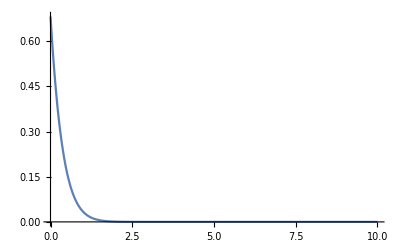

```mathematica
nd=200; ns=300; b=3.;k=5.32635-b;ndR=2;
expYSteadyVar=expYSteady[b, nd, ndR];
expY2SteadyVar=expY2Steady[b, nd, ndR];
ASteadyVar=ASteady[b, nd, ndR];
muOverSigmaSteadyVar=ansatzMuOverSigma[expYSteadyVar,expY2SteadyVar,ASteadyVar];
sigmaSteadyVar=ansatzSigma[expYSteadyVar,expY2SteadyVar,ASteadyVar, muOverSigmaSteadyVar];
muSteadyVar = ansatzMu[muOverSigmaSteadyVar, sigmaSteadyVar];
Plot[ansatzProbY[Y, muSteadyVar, sigmaSteadyVar, ASteadyVar], {Y, 0.001, 10}, PlotRange->All]
th=muSteadyVar-√2 sigmaSteadyVar InverseErf[(0.01(1+Erf[muSteadyVar/(√2 sigmaSteadyVar)]))/(1-ASteadyVar)-1];
```

```mathematica
tStart=1000; tEnd=1600;tStep=100;
tList=Table[t, {t, tStart, tEnd, tStep}];
fList=Thread[fInt[b, k, nd, ndR, ns, tList]];
expYIList=Thread[expYI[b, fList, nd, ndR]];
expY2IList=Thread[expY2I[b, fList, nd, ndR]];
AIList=Thread[AI[b, fList, nd, ndR]];
expYIIList=Thread[expYII[b, fList, k, nd, ndR]];
expY2IIList=Thread[expY2II[b, fList, k, nd, ndR]];
AIIList=Thread[AII[b, fList, k, nd, ndR]];
muOverSigmaIList=MapThread[ansatzMuOverSigma, {expYIList,expY2IList, AIList}];
sigmaIList=Thread[ansatzSigma[expYIList,expY2IList, AIList, muOverSigmaIList]];
muIList=Thread[ansatzMu[sigmaIList, muOverSigmaIList]];
muOverSigmaIIList=MapThread[ansatzMuOverSigma, {expYIIList,expY2IIList, AIIList}];
sigmaIIList=Thread[ansatzSigma[expYIIList,expY2IList, AIIList, muOverSigmaIIList]];
muIIList=Thread[ansatzMu[sigmaIIList, muOverSigmaIIList]];
falseNegativeList=Thread[falseNegative[th, muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList]];
```

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

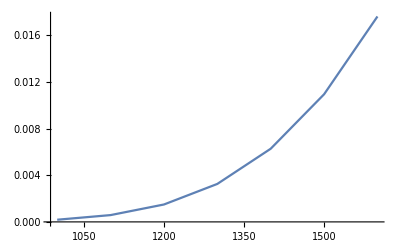

```mathematica
ListLinePlot[Transpose[{tList, falseNegativeList}]]
```